### Fisheries management In this Figure we plot the profit for the ecologically enlightened and for the evolutionary enlightened manager. For details about the calculation of the Nash and Stackelberg strategies and outcomes, see Salvioli, M; Dubbeldam, J; Staňková, K; Brown, J.S.(2021). Fisheries management as a Stackelberg Evolutionary Game: Finding an evolutionarily enlightened strategy. Plos one,16(1),e0245255.

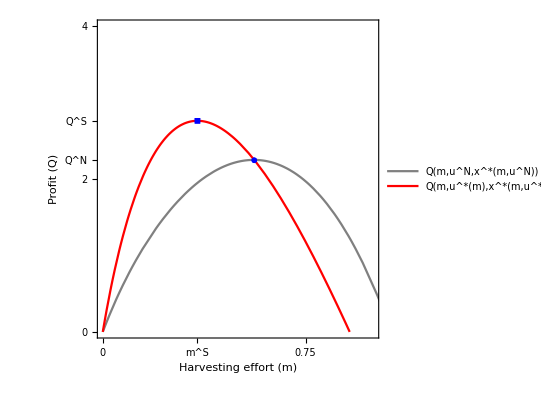

```mathematica
ClearAll;
SetOptions[Plot,BaseStyle->{FontFamily->"CMU Sans Serif",FontSize->18}];

s=1;
g=5;
R=4;
d=0.2;
z=3;
c=5;
u^S=9.09;
u^N=6.58;

(*The coordinates and outcomes of the Nash and Stackelberg equilibria are (m^N=0.56,u^N=6.58,Q^N=2.24485) and (m^S=0.350012,u^S=9.09,Q^S=2.76147)  *)
ProfitFunction[s_,u_,R_,m_,z_,g_,d_,c_]:=(m*R)/(u*(m+d))*Log[1/(m+d) s*u*Exp[(-m*(u-z))/g]*Exp[(-d*u)/g]]*(((m+d)*z+g)/Exp[(-(m+d)*(u-z))/g]-g)-(c*m);

EcoEnlightened=Plot[ProfitFunction[s,u^N,R,m,z,g,d,c],{m,0,10},PlotRange->{{0,1},{0,4}},PlotStyle->{Gray},AspectRatio->1,PlotLegends->{"Q(m,u^N,x^*(m,u^N))"}];

EvoEnlightened=Plot[ProfitFunction[s,g/(m+d),R,m,z,g,d,c],{m,0,g/z-d},PlotRange->{{0,1},{0,4}},PlotStyle->{Red},AspectRatio->1,PlotLegends->{"Q(m,u^*(m),x^*(m,u^*(m)))"}];

NashOutcome=ListPlot[{{0.56,2.24485}},PlotMarkers->{{●,14}},PlotStyle->{Blue}];

StackOutcome=ListPlot[{{0.350012,2.76147}},PlotMarkers->{{■,15}},PlotStyle->{Blue}];

Show[{EcoEnlightened,LoStack1,NashOutcome,StackOutcome},Frame->{{True,False},{True,False}},FrameLabel->{{"Profit (Q)",None},{"Harvesting effort (m)",None}},FrameTicks->{{{0,2,{2.24485,"Q^N"},{2.76147,"Q^S"},4},None},{{0,0.25,{0.350012,"m^S"},{0.56,"m^N"},0.75,1},None}},LabelStyle->Directive[Black,18]]
```